```mathematica
SetDirectory["D:\\newLight3"]
```

D:\newLight3

```mathematica
cellColours={RGBColor[0.462745, 0.862745, 0.482353],RGBColor[0.37, 0.21, 0.],RGBColor[0.21, 0.21, 0.21],RGBColor[0., 0.73, 0.8200000000000001],RGBColor[1., 0.91, 0.04],RGBColor[0., 0.3, 0.8200000000000001],RGBColor[0.86, 0.74, 0.],RGBColor[0.98, 0.5700000000000001, 1.]};
```

```mathematica
GetOrgCells[ org_,frameNo_]:=Module[{path,file,headings,applyHeading,items},
path = StringForm["output\\frame``.csv",frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
Select[items,("o"/.#)==org&]
]
```

Use genome file to find out step of birth and (if dead) death, show frame in between (rounded to nearest saved)

```mathematica
GetOrgCells[org_]:=Module[{sMin, sMax,o,s},
sMin = "step"/.GetOrganism[org];
sMax=Check["step"/.GetOrgDeath[org],sMin]//Quiet;
o={};
For[i=0,Length[o]==0,i++,
s = Round[(sMin+sMax)/2,10^i];
o=Check[GetOrgCells[org,s],{}]//Quiet;
If[s==0,Break[];] (* No frame with organism saved *)
];
{s,o}
]
```

Should no organisms be found, it would be better to search both beneath and above middle life.

```mathematica
VisualizeOrg[org_]:=Module[{},
Graphics3D[Riffle[
Sphere[{"x","y","z"},"r"]/.org,
cellColours⟦#+1⟧&/@("ct"/.org)
], Boxed->False]
]
```

```mathematica
GetOrganism[orgNo_]:=With[{path=StringForm["organisms\\org``.json",orgNo]//ToString},
Import[path]
]
```

```mathematica
GetOrgDeath[orgNo_]:=With[{path=StringForm["orgDeaths\\org``.json",orgNo]//ToString},
Import[path]
]
```

```mathematica
GetOrgInfo[orgNo_]:=Module[{visStep,org,birth,death},
{visStep,org}=GetOrgCells[orgNo];
birth=GetOrganism[orgNo];
death=GetOrgDeath[orgNo]//Quiet;
{
"vis"-> VisualizeOrg[org],
"id"-> orgNo,
"birthStep"-> "step"/.birth,
"visStep"-> visStep,
"deathStep"->Check["step"/.death,"Still alive"],
"generation"-> (getAncestors[orgNo]//Length)
}
]
```

```mathematica
GetOrgInfo[2000]//Column
```

vis→-Graphics3D-
birthStep→85462
visStep→90000
deathStep→90448
generation→25

```mathematica
getAncestors[org_]:=NestWhileList["parent"/.GetOrganism[#]&,org,#>0&];
```

```mathematica
RelationsGraph[orgs_]:=Module[{os,o1,o2,lca},
If[Length[orgs]<2,Return[Graph[orgs,{}]]];
os=Sort[orgs,Greater];
{o1,o2}=Take[os,2];
lca=GetLCA[o1,o2];
GraphUnion[
{lca-> o1,lca-> o2},
RelationsGraph[Append[Drop[os,2],lca]],
VertexLabels->"Name"
]
];
```

```mathematica
VisualizeAllAncestors[org_]:=ParallelMap[InfoCard[GetOrgInfo[#]]&,getAncestors[org]];
```

```mathematica
GetLCA[o1_,o2_]:=Module[{a1,a2},
a1=o1;a2=o2;
While[a1≠a2,If[a1>a2,
a1="parent"/.GetOrganism[a1],
a2="parent"/.GetOrganism[a2]
]];
a1
];
```

```mathematica
GetLivingOrganisms[frameNo_]:=Module[{path,file,headings,items,applyHeading,organisms},
path = StringForm["output\\frame``.csv",frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
organisms="o"/.items//DeleteDuplicates;
Select[organisms,#>=0&]
]
```

```mathematica
InfoCard[vis_]:=TableForm[{{"vis"/.vis, {{"ID", "id"/.vis}, {"Birth", "birthStep"/.vis}, {"Vis", "visStep"/.vis}, {"Death", "deathStep"/.vis}, {"Gen", "generation"/.vis}}}},TableSpacing->{0, 0}]
```

```mathematica
InfoTree[orgs_]:=Module[{tree,root,nodes},
tree=RelationsGraph[orgs];
nodes=VertexList[tree];
root=Ordering[nodes,1]//First;
TreePlot[tree,Automatic,
root,
VertexRenderingFunction-> (Inset[InfoCard[GetOrgInfo[nodes⟦#2⟧]],#1]&),
ImageSize->Full,VertexLabeling->True
]
];
```

```mathematica
living= GetLivingOrganisms[730000];
Length[living]
```

5829

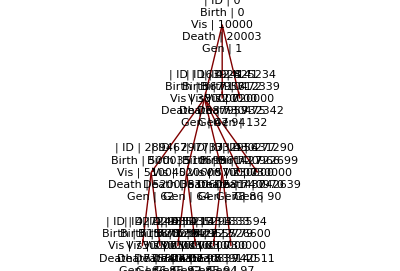

```mathematica
InfoTree[RandomChoice[living,10]]
```

```mathematica
VisualizeAllAncestors[10]//Row
```

-Graphics3D- | ID | 10
Birth | 13702
Vis | 14050
Death | 14400
Gen | 3-Graphics3D- | ID | 1
Birth | 6437
Vis | 15250
Death | 24058
Gen | 2-Graphics3D- | ID | 0
Birth | 0
Vis | 10000
Death | 20003
Gen | 1

```mathematica
VisualizeAllAncestors[435213]
```

Riffle::list: List expected at position 1 in Riffle[Sphere[{x,y,z},r],ct].

{-Graphics3D- | ID | 435213
Birth | 729422
Vis | 730000
Death | 735598
Gen | 92,-Graphics3D- | ID | 431278
Birth | 722679
Vis | 730000
Death | 733554
Gen | 91,-Graphics3D- | ID | 426900
Birth | 715307
Vis | 720000
Death | 725838
Gen | 90,-Graphics3D- | ID | 416463
Birth | 696832
Vis | 710000
Death | 716835
Gen | 89,-Graphics3D- | ID | 411012
Birth | 687472
Vis | 700000
Death | 707475
Gen | 88,-Graphics3D- | ID | 408756
Birth | 683504
Vis | 690000
Death | 697161
Gen | 87,-Graphics3D- | ID | 403067
Birth | 673964
Vis | 680000
Death | 693967
Gen | 86,-Graphics3D- | ID | 400656
Birth | 669762
Vis | 680000
Death | 689765
Gen | 85,-Graphics3D- | ID | 395411
Birth | 660788
Vis | 670000
Death | 676242
Gen | 84,-Graphics3D- | ID | 387675
Birth | 648147
Vis | 660000
Death | 668150
Gen | 83,-Graphics3D- | ID | 385438
Birth | 644343
Vis | 650000
Death | 664346
Gen | 82,-Graphics3D- | ID | 382958
Birth | 640313
Vis | 650000
Death | 659022
Gen | 81,-Graphics3D- | ID | 380816
Birth | 636852
Vis | 650000
Death | 654983
Gen | 80,-Graphics3D- | ID | 378847
Birth | 633396
Vis | 640000
Death | 648676
Gen | 79,-Graphics3D- | ID | 367915
Birth | 614891
Vis | 620000
Death | 634894
Gen | 78,-Graphics3D- | ID | 360288
Birth | 603019
Vis | 610000
Death | 623022
Gen | 77,-Graphics3D- | ID | 357547
Birth | 598825
Vis | 610000
Death | 618515
Gen | 76,-Graphics3D- | ID | 355042
Birth | 595186
Vis | 610000
Death | 615189
Gen | 75,-Graphics3D- | ID | 352333
Birth | 591248
Vis | 600000
Death | 611251
Gen | 74,-Graphics3D- | ID | 349480
Birth | 587072
Vis | 590000
Death | 597732
Gen | 73,-Graphics3D- | ID | 346830
Birth | 583162
Vis | 590000
Death | 603165
Gen | 72,-Graphics3D- | ID | 341892
Birth | 575263
Vis | 590000
Death | 595266
Gen | 71,-Graphics3D- | ID | 334960
Birth | 564646
Vis | 570000
Death | 584649
Gen | 70,-Graphics3D- | ID | 330568
Birth | 557732
Vis | 570000
Death | 577735
Gen | 69,-Graphics3D- | ID | 326139
Birth | 550900
Vis | 560000
Death | 570903
Gen | 68,-Graphics3D- | ID | 321401
Birth | 543616
Vis | 550000
Death | 563619
Gen | 67,-Graphics3D- | ID | 318777
Birth | 539841
Vis | 549840
Death | 559844
Gen | 66,-Graphics3D- | ID | 311606
Birth | 529531
Vis | 539530
Death | 549534
Gen | 65,-Graphics3D- | ID | 297737
Birth | 510599
Vis | 520600
Death | 530602
Gen | 64,-Graphics3D- | ID | 292350
Birth | 503644
Vis | 513650
Death | 523648
Gen | 63,-Graphics3D- | ID | 289467
Birth | 500035
Vis | 510040
Death | 520038
Gen | 62,-Graphics3D- | ID | 277674
Birth | 486259
Vis | 490000
Death | 501209
Gen | 61,-Graphics3D- | ID | 274538
Birth | 482459
Vis | 490000
Death | 502462
Gen | 60,-Graphics3D- | ID | 262842
Birth | 469659
Vis | 480000
Death | 489662
Gen | 59,-Graphics3D- | ID | 247813
Birth | 452838
Vis | 460000
Death | 472842
Gen | 58,-Graphics3D- | ID | 244100
Birth | 448619
Vis | 450000
Death | 458857
Gen | 57,-Graphics3D- | ID | 227968
Birth | 431163
Vis | 440000
Death | 451166
Gen | 56,-Graphics3D- | ID | 218585
Birth | 420847
Vis | 430000
Death | 432051
Gen | 55,-Graphics3D- | ID | 211149
Birth | 413490
Vis | 420000
Death | 433493
Gen | 54,-Graphics3D- | ID | 203008
Birth | 405315
Vis | 420000
Death | 425318
Gen | 53,-Graphics3D- | ID | 199021
Birth | 401320
Vis | 410000
Death | 421323
Gen | 52,-Graphics3D- | ID | 192235
Birth | 395118
Vis | 410000
Death | 415122
Gen | 51,-Graphics3D- | ID | 186144
Birth | 389497
Vis | 400000
Death | 409500
Gen | 50,-Graphics3D- | ID | 178621
Birth | 381687
Vis | 390000
Death | 391826
Gen | 49,-Graphics3D- | ID | 175015
Birth | 378316
Vis | 390000
Death | 398319
Gen | 48,-Graphics3D- | ID | 163928
Birth | 367956
Vis | 380000
Death | 387959
Gen | 47,-Graphics3D- | ID | 147599
Birth | 351527
Vis | 360000
Death | 370885
Gen | 46,-Graphics3D- | ID | 133113
Birth | 337228
Vis | 350000
Death | 357231
Gen | 45,-Graphics3D- | ID | 119045
Birth | 326190
Vis | 340000
Death | 346193
Gen | 44,-Graphics3D- | ID | 108849
Birth | 316980
Vis | 330000
Death | 336983
Gen | 43,-Graphics3D- | ID | 98747
Birth | 306768
Vis | 320000
Death | 324816
Gen | 42,-Graphics3D- | ID | 96098
Birth | 304157
Vis | 310000
Death | 322206
Gen | 41,-Graphics3D- | ID | 91599
Birth | 300613
Vis | 310000
Death | 310275
Gen | 40,-Graphics3D- | ID | 83184
Birth | 293389
Vis | 300000
Death | 301577
Gen | 39,-Graphics3D- | ID | 79692
Birth | 289714
Vis | 300000
Death | 307929
Gen | 38,-Graphics3D- | ID | 67345
Birth | 279610
Vis | 290000
Death | 292117
Gen | 37,-Graphics3D- | ID | 64477
Birth | 277260
Vis | 280000
Death | 288317
Gen | 36,-Graphics3D- | ID | 60814
Birth | 274230
Vis | 280000
Death | 294233
Gen | 35,-Graphics3D- | ID | 56400
Birth | 270354
Vis | 280000
Death | 284606
Gen | 34,-Graphics3D- | ID | 49781
Birth | 264318
Vis | 270000
Death | 276747
Gen | 33,-Graphics3D- | ID | 46019
Birth | 260299
Vis | 270000
Death | 280303
Gen | 32,-Graphics3D- | ID | 40796
Birth | 253238
Vis | 260000
Death | 273241
Gen | 31,-Graphics3D- | ID | 35365
Birth | 244669
Vis | 250000
Death | 257886
Gen | 30,-Graphics3D- | ID | 33776
Birth | 242041
Vis | 0
Death | 247138
Gen | 29,-Graphics3D- | ID | 30339
Birth | 236062
Vis | 240000
Death | 250583
Gen | 28,-Graphics3D- | ID | 27017
Birth | 229623
Vis | 240000
Death | 249626
Gen | 27,-Graphics3D- | ID | 24653
Birth | 224687
Vis | 230000
Death | 244101
Gen | 26,-Graphics3D- | ID | 21213
Birth | 217001
Vis | 230000
Death | 237004
Gen | 25,-Graphics3D- | ID | 18862
Birth | 211018
Vis | 220000
Death | 231021
Gen | 24,-Graphics3D- | ID | 16744
Birth | 204978
Vis | 210000
Death | 224981
Gen | 23,-Graphics3D- | ID | 11975
Birth | 186867
Vis | 200000
Death | 206870
Gen | 22,-Graphics3D- | ID | 10928
Birth | 181861
Vis | 190000
Death | 198586
Gen | 21,-Graphics3D- | ID | 9963
Birth | 176511
Vis | 190000
Death | 195044
Gen | 20,-Graphics3D- | ID | 8186
Birth | 164632
Vis | 170000
Death | 184636
Gen | 19,-Graphics3D- | ID | 6786
Birth | 152236
Vis | 160000
Death | 172239
Gen | 18,-Graphics3D- | ID | 6280
Birth | 146428
Vis | 150000
Death | 155002
Gen | 17,-Graphics3D- | ID | 5729
Birth | 140113
Vis | 150000
Death | 160116
Gen | 16,-Graphics3D- | ID | 5409
Birth | 136283
Vis | 150000
Death | 154503
Gen | 15,-Graphics3D- | ID | 4690
Birth | 127406
Vis | 140000
Death | 147409
Gen | 14,-Graphics3D- | ID | 3323
Birth | 110209
Vis | 120000
Death | 130212
Gen | 13,-Graphics3D- | ID | 2280
Birth | 91109
Vis | 100000
Death | 111113
Gen | 12,-Graphics3D- | ID | 2082
Birth | 87606
Vis | 90000
Death | 95553
Gen | 11,-Graphics3D- | ID | 1793
Birth | 80555
Vis | 90000
Death | 100558
Gen | 10,-Graphics3D- | ID | 998
Birth | 65095
Vis | 80000
Death | 85098
Gen | 9,-Graphics3D- | ID | 944
Birth | 63088
Vis | 70000
Death | 83091
Gen | 8,-Graphics3D- | ID | 609
Birth | 51107
Vis | 60000
Death | 71111
Gen | 7,-Graphics3D- | ID | 405
Birth | 43060
Vis | 50000
Death | 63063
Gen | 6,-Graphics3D- | ID | 238
Birth | 35226
Vis | 45230
Death | 55229
Gen | 5,-Graphics3D- | ID | 42
Birth | 21951
Vis | 31950
Death | 41954
Gen | 4,-Graphics3D- | ID | 14
Birth | 14513
Vis | 24510
Death | 34516
Gen | 3,-Graphics3D- | ID | 1
Birth | 6437
Vis | 15250
Death | 24058
Gen | 2,-Graphics3D- | ID | 0
Birth | 0
Vis | 10000
Death | 20003
Gen | 1}